## Examples used during the lectures

## Day 2

```mathematica
w1[x,x]^q1 w2[x,x]^q2 == 1
```

w1[x,x]^q1 w2[x,x]^q2==1

```mathematica
D[w1[y,x]^q1 w2[y,x]^q2,y] /. y-> x 
% == q1 w1[x,x]^(-1+q1) w2[x,x]^q2 Derivative[1,0][w1][x,x]+q2 w1[x,x]^q1 w2[x,x]^(-1+q2) Derivative[1,0][w2][x,x] ;
```

```mathematica
w1[x,x]^q1 w2[x,x]^(-1+q2) == w1[x,x]^q1 w2[x,x]^q2/w2[x,x]  //Simplify 
% == w1[x,x]^q1 w2[x,x]^q2/w2[x,x] == 1/w2[x,x]
q2 w1[x,x]^q1 w2[x,x]^(-1+q2) Derivative[1,0][w2][x,x]  == q2 (Derivative[1,0][w2][x,x])/w2[x,x]
```

```mathematica
D[Log[w2[y,x]],y]/.y->x
```

(w2^(1,0)[x,x])/w2[x,x]

True

### Time heterogeneous population

```mathematica
Clear["Global`*"]
```

Wright - Fisher model fluctuating between environment 1 and 2 with trait optima at -1 (with occurrence p) and 1 (with occurrence 1-p)

```mathematica
ρ=(Exp[-1/2((y+1)/σ1)^2]/Exp[-1/2((x+1)/σ1)^2])^q1(Exp[-1/2((y-1)/σ2)^2]/Exp[-1/2((x-1)/σ2)^2])^q2;
```

```mathematica
S = D[ρ,y] /. y-> x  //Simplify
```

-(q1 (1+x))/σ1^2+(q2-q2 x)/σ2^2

```mathematica
S == -(1+x)/(2 σ1^2)+(1-x)/(2 σ2^2) ;
```

```mathematica
sing = Flatten@Solve[S ==0,x]
```

{x→(q2 σ1^2-q1 σ2^2)/(q2 σ1^2+q1 σ2^2)}

```mathematica
J = D[S,x] /.sing
```

-1/(2 σ1^2)-1/(2 σ2^2)

```mathematica
H = D[ρ,y,y] /. y-> x  /. s1-> s /. s2-> s /.p2->1-p1 ;
%  /.sing //Simplify
```

-1/(2 σ1^2)-1/(2 σ2^2)

### Second order derivative

```mathematica
D[Log[wc[y,x]],y,y]
```

-((wc^(1,0)[y,x])^2)/wc[y,x]^2+(wc^(2,0)[y,x])/wc[y,x]

### High and low quality individuals populations

```mathematica
Clear["Global`*"]
```

```mathematica
w11 = k f1 pH  Exp[-1/2((y+1)/σ)^2]/Exp[-1/2((x+1)/σ)^2] /. k->1/(1+(f1-1) pH) ;
w21 = k f1 (1-pH)Exp[-1/2((y+1)/σ)^2]/Exp[-1/2((x+1)/σ)^2] /. k->1/(1+(f1-1) pH);
w12 =   k  pH  Exp[-1/2((y-1)/σ)^2]/Exp[-1/2((x-1)/σ)^2]/. k->1/(1+(f1-1) pH);
w22 = k (1-pH) Exp[-1/2((y-1)/σ)^2]/Exp[-1/2((x-1)/σ)^2] /. k->1/(1+(f1-1) pH);
```

```mathematica
W  = {{w11,w12},{w21,w22}} ;
```

```mathematica
W0 = W /. y-> x //Simplify 
Eigenvalues[W0][[2]] ==1 ;
q0 = Eigenvectors[W0][[2]] ; 
q0 = q0 /Total[q0]//Simplify
```

{{(f1 pH)/(1+(-1+f1) pH),pH/(1+(-1+f1) pH)},{(f1 (1-pH))/(1+(-1+f1) pH),(1-pH)/(1+(-1+f1) pH)}}

{pH,1-pH}

```mathematica
v0.q0 == 1//Simplify
W0.q0 ==q0 //Simplify
v0.W0 ==v0  //Simplify
```

True

True

True

```mathematica
q0 == {pH,1-pH} 
v0 ==k {f1,1}  /. k->1/(1+(f1-1) pH) //Simplify
```

True

True

```mathematica
S = v0.(D[W,y]/.y->x).q0  //Simplify 
S //Simplify
```

-(-1+x+pH (1+f1-x+f1 x))/((1+(-1+f1) pH) σ^2)

-(-1+x+pH (1+f1-x+f1 x))/((1+(-1+f1) pH) σ^2)

```mathematica
sing = Flatten@Solve[S ==0,x]//Simplify ;
(x/. sing)  == (1-(1+f1) pH)/(1+(f1-1) pH)
```

True

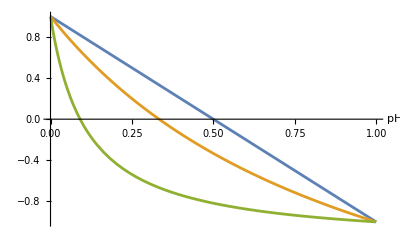

```mathematica
Plot[Evaluate[(1-(1+f1) pH)/(1+(f1-1) pH)  /.f1->{1,2,10}],{pH,0,1},AxesLabel->Automatic]
```

```mathematica
J = D[S,x] /.sing
```

-1/σ^2

```mathematica
v0.(D[W,y,y]/.y->x).q0   /. y-> x ;
Hw = %  /.sing  //Simplify
```

-((-1+pH)^2 σ^2+f1^2 pH^2 σ^2-2 f1 (-1+pH) pH (-2+σ^2))/((1+(-1+f1) pH)^2 σ^4)

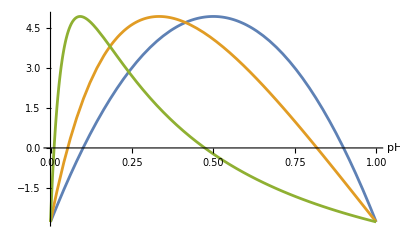

```mathematica
Plot[Evaluate[-((-1+pH)^2 σ^2+f1^2 pH^2 σ^2-2 f1 (-1+pH) pH (-2+σ^2))/((1+(-1+f1) pH)^2 σ^4)/. σ->0.6  /.f1->{1,2,10}],{pH,0,1},AxesLabel->Automatic]
```

```mathematica
q1 = Eigenvectors[W][[2]] ; 
q1 = q1 /Total[q1]//Simplify /.y->x //Simplify
```

{pH,1-pH}

```mathematica
v0.(D[W,y]/.y->x).(D[q1,y]/.y->x)   /. y-> x ;
%  /.sing  /. m12->m  /. m21 ->m /.s1->s/.s2->s  ;
Hq =  Assuming[s>0&& 0<m<1 && x∈Reals &&y∈Reals,Simplify[%]]
```

0

### Age structure

```mathematica
Clear["Global`*"];
```

```mathematica
(*ages*)
a={1,2,3,4,5,6,7};
(*Probabilities of survival*)
s={0.46,0.77,0.65,0.67,0.64,0.88,0};
(*Survival until*)
l=Delete[FoldList[Times,1,s],-1] ;
(*fecundities*)
b0={0.32,0.57,0.57,0.57,0.57,0.57,0.57};
R00 = l.b0  ;
(* fecundities scaled *)
b=b0/ R00

(* Lifetime reproductive success *)
R0= l.b  

(* Reproductive values *)
v = Table[(l[[j;;7]].b[[j;;7]])/l[[j]],{j,1,7}]
```

{0.288538,0.513958,0.513958,0.513958,0.513958,0.513958,0.513958}

1.

{1.,1.54666,1.34117,1.27263,1.13235,0.96624,0.513958}

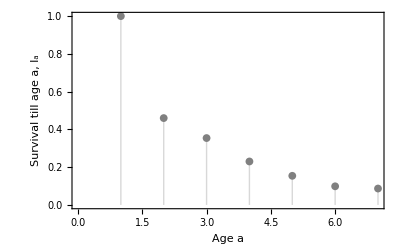

/Users/cmullon/Dropbox/Teaching/Summer_School/Course_Material_2025/Survivaltill.png

```mathematica
ListPlot[l,Filling->Axis,PlotStyle->Directive[Gray,Opacity[1]],Frame->{{True,False},{True,False}},FrameLabel->{"Age a","Survival till age a, l_a"},PlotMarkers-> {"●", 8},LabelStyle->Directive[ 14] ]
Export["/Users/cmullon/Dropbox/Teaching/Summer_School/Course_Material_2025/Survivaltill.png",%]
```

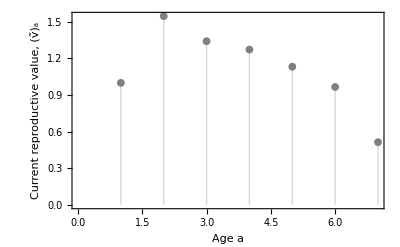

/Users/cmullon/Dropbox/Teaching/Summer_School/Course_Material_2025/RepValueAge.png

```mathematica
ListPlot[v,Filling->Axis,PlotStyle->Directive[Gray,Opacity[1]],Frame->{{True,False},{True,False}},FrameLabel->{"Age a","Current reproductive value, (ṽ)_a"},PlotMarkers-> {"●", 8},LabelStyle->Directive[ 14] ]
Export["/Users/cmullon/Dropbox/Teaching/Summer_School/Course_Material_2025/RepValueAge.png",%]
```